```mathematica
Avg=33
dt={34,15,7,29,47,30,41,61}
D1=0.2321
D2=0.2151
D3=0.2041
P1={12,2,5,5,11,7,9,17}
P2={8,10,15,31,6,1,3,9}
P3={8,4,8,16,12,7,9,15}
FindFit[dt,Avg* ⅇ^Sin[p+t w] ((C1 P1[[t]])/Log[1+D1]+(C2 P2[[t]])/Log[1+D2]+(C3  P3[[t]])/Log[1+D3])*(x Family[[t]]+Culture[[t]]),{p,w,C1,C2,C3,x},t]
```

33

{34,15,7,29,47,30,41,61}

0.2321

0.2151

0.2041

{12,2,5,5,11,7,9,17}

{8,10,15,31,6,1,3,9}

{8,4,8,16,12,7,9,15}

Part::pkspec1: The expression t cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindFit::nrlnum: The function value {-34.+11602.9 (1. B1+B2),-15.+3133.09 (1. B1+B2),-7.+2229.78 (1. B1+B2),-29.+3405.34 (1. B1+B2),-47.+3696.1 (1. B1+B2),-30.+4860.72 (1. B1+B2),-41.+9494.44 (1. B1+B2),-61.+10384.9 (1. B1+B2)} is not a list of real numbers with dimensions {8} at {p,w,C1,C2,C3,x} = {1.,1.,1.,1.,1.,1.}.

FindFit[{34,15,7,29,47,30,41,61},33 ⅇ^Sin[p+t w] (B2+B1 x) (5.38409 C3 {8,4,8,16,12,7,9,15}⟦t⟧+5.13278 C2 {8,10,15,31,6,1,3,9}⟦t⟧+4.79111 C1 {12,2,5,5,11,7,9,17}⟦t⟧),{p,w,C1,C2,C3,x},t]

Part::pkspec1: The expression 1.00014 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

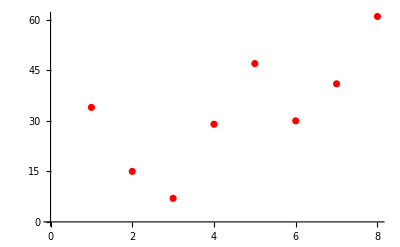

```mathematica
Show[ListPlot[dt,PlotStyle->Red],Plot[Avg ⅇ^Sin[p+t w] ((C1 P1⟦t⟧)/Log[1+D1]+(C2 P2⟦t⟧)/Log[1+D2]+(C3 P3⟦t⟧)/Log[1+D3])/.{p->2.8604548193592545,w->0.811307935970819,C1->0.04023122465662978,C2->0.016117209010432974,C3->-0.028788597768872},{t,1,8}]]
```